```mathematica
all=20
Table[(Binomial[all,i]*Binomial[all,10-i])/Binomial[2all,10],{i,9}]
```

20

{50/12617,1425/50468,17100/164021,72675/328042,46512/164021,72675/328042,17100/164021,1425/50468,50/12617}

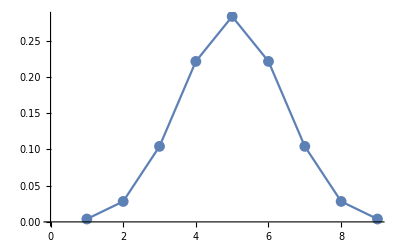

```mathematica
ListLinePlot[{50/12617,1425/50468,17100/164021,72675/328042,46512/164021,72675/328042,17100/164021,1425/50468,50/12617},Mesh->All]
```

```mathematica
this is a Hypergeometric Distribution
```

```mathematica
p=0.5
all=10
Table[Binomial[all,i]p^i (1-p)^(all-i),{i,9}]
```

0.5

10

{0.00976563,0.0439453,0.117188,0.205078,0.246094,0.205078,0.117188,0.0439453,0.00976563}

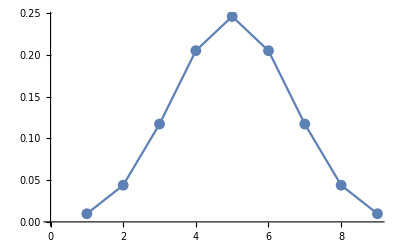

```mathematica
ListLinePlot[{0.009765625,0.0439453125,0.1171875,0.205078125,0.24609375,0.205078125,0.1171875,0.0439453125,0.009765625},Mesh->All]
```

```mathematica
this is a Binomial Distribution
```